```mathematica
Clear["Global`*"]
k:=1;g:=-1;h:=1/n;ρ:=0.001;n:=14
s[x_]=0.96-0.25(x-0.5)^2
```

0.96-0.25 (-0.5+x)^2

```mathematica
yvec=Table[Subscript[y, i],{i,1,n-1}];
λvec=Table[Subscript[λ, i],{i,1,n-1}];
xs:=Table[(1/n)i,{i,1,n-1}]
```

```mathematica
Eq1:={Piecewise[{{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1+λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]]),λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])≤0},{(-1+2*yvec[[1]]-yvec[[2]])/h^2+1,λvec[[1]]+ρ*(yvec[[1]]-s[xs[[1]]])>0}}]};
Eqn:={Piecewise[{{(-1+2*yvec[[n-1]]-yvec[[n-2]])/h^2+1+λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]]),λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])≤0},{(-1+2*yvec[[n-1]]-yvec[[n-2]])/h^2+1,λvec[[n-1]]+ρ*(yvec[[n-1]]-s[xs[[n-1]]])>0}}]};
Eqs1:=Table[Piecewise[{{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1+λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]]),λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{(-yvec[[i-1]]+2*yvec[[i]]-yvec[[i+1]])/h^2+1,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,2,n-2}];
Eqs2:=Table[Piecewise[{{yvec[[i]]-s[xs[[i]]], λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])≤0},{-λvec[[i]]/ρ,λvec[[i]]+ρ*(yvec[[i]]-s[xs[[i]]])>0}}],{i,1,n-1}]
```

```mathematica
DfDy=Join[Eq1,Eqs1,Eqn,Eqs2];
D2fDyy=D[ DfDy,{Join[yvec,λvec],1} ];
Table[Subscript[y, i]=1,{i,1,n-1}];Table[Subscript[λ, i]=0,{i,1,n-1}];
i=0;
While[ Sqrt[DfDy.DfDy]>10^-8&&i≤25,
dy=-Inverse[D2fDyy].DfDy;
Table[Subscript[y, i]=Subscript[y, i]+dy[[i]],{i,1,n-1}];
Table[Subscript[λ, i]=Subscript[λ, i]+dy[[n-1+i]],{i,1,n-1}];
i=i+1;
];
```

```mathematica
D2fDyy//MatrixForm
```

(392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -196 | 392.001 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -196 | 392.001 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -196 | 392.001 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -196 | 392.001 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -196 | 392.001 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -196 | 392 | -196 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -196 | 392 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000. | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -1000.)

```mathematica
xplot:=Join[{0},xs,{1}];yplot:=Join[{1},yvec,{1}]
```

```mathematica
str:=ListLinePlot[Transpose[{xplot,yplot}],Frame->True,PlotStyle->{Orange}]
```

```mathematica
st:=RegionPlot[{y<s[x]&&y≥0},{x,0,1},{y,0,1},ColorFunction->Function[{x,y},ColorData["PigeonTones"][Sin[x]Sin[y]]],BoundaryStyle->None]
```

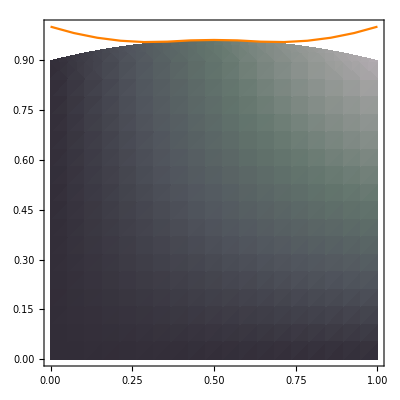

```mathematica
Show[st,str,AspectRatio->1,PlotRange->All]
```